Exercises for Section 27 | Applying Functions Repeatedly

Make a list of the results of nesting Blur up to 10 times, starting with a rasterized size-30 “X”. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Rasterize["X", ImageSize->30]
```

-Graphics-

```mathematica
Graphics["X",ImageSize->30]
```

-Graphics-

```mathematica
NestList[Blur,Rasterize[Style["X",30]],10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NestList
```

Syntax::tsntxi: "NestList?" is incomplete; more input is needed.

Start with x, then make a list by nestedly applying Framed up to 10 times, using a random background color each time. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
NestList[Style[#,Background->RandomColor[]],#,10]&@Style["x"]
```

{x,x[x],x[x[x]],x[x[x[x]]],x[x[x[x[x]]]],x[x[x[x[x[x]]]]],x[x[x[x[x[x[x]]]]]],x[x[x[x[x[x[x[x]]]]]]],x[x[x[x[x[x[x[x[x]]]]]]]],x[x[x[x[x[x[x[x[x[x]]]]]]]]],x[x[x[x[x[x[x[x[x[x[x]]]]]]]]]]}

```mathematica
NestList[Framed[#,Background->RandomColor[]]&,x,10]
```

{x,x,x,x,x,x,x,x,x,x,x}

Start with a size-50 “A”, then make a list of nestedly applying a frame and a random rotation 5 times. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
NestList[Framed,Style["A",50],5]
```

{A,A,A,A,A,A}

```mathematica
NestList[Framed[#,Background->RandomColor[]]&,Style["A",50],5]
```

{A,A,A,A,A,A}

```mathematica
NestList[Rotate[Framed[#],RandomReal[{0,360°}]]&,Style["A",50],5]
```

{A,A,A,A,A,A}

Make a line plot of 100 iterations of the logistic map iteration 4 #(1-#)&, starting from 0.2. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot@NestList[4#(1-#)&,0.2,100]
```

-Graphics-

Find the numerical value of the result from 30 iterations of 1+1/#& starting from 1. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Last[NestList[1+1/#&,1,30]]//N
```

1.61803

Create a list of the first 10 powers of 3 (starting at 0) by nested multiplication. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
NestList[3*#&,1,10]
```

{1,3,9,27,81,243,729,2187,6561,19683,59049}

Make a list of the result of nesting the (Newton’s method) function (#+2/#)/2& up to 5 times starting from 1.0, and then subtract √2from all the results. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
NestList[(#+2/#)/2&,1.0,5]-Sqrt[2]
```

{-0.414214,0.0857864,0.0024531,2.1239×10^-6,1.59472×10^-12,-2.22045×10^-16}

Make graphics of a 1000-step 2D random walk which starts at {0,0}, and in which at each step a pair of random numbers between −1 and +1 are added to the coordinates. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

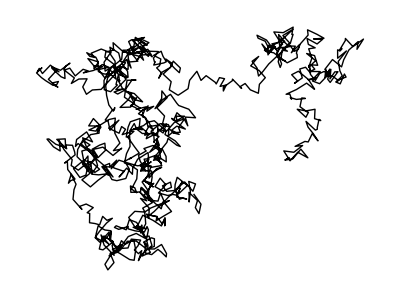

```mathematica
Graphics@Line[NestList[#+RandomReal[{-1,1},2]&,{0,0},1000]]
```

Make an array plot of 50 steps of Pascal’s triangle modulo 2 by starting from {1} and nestedly joining {0} at the beginning and at the end, and adding these results together modulo 2. |

EXPECTED OUTPUT »

-Graphics- | ×

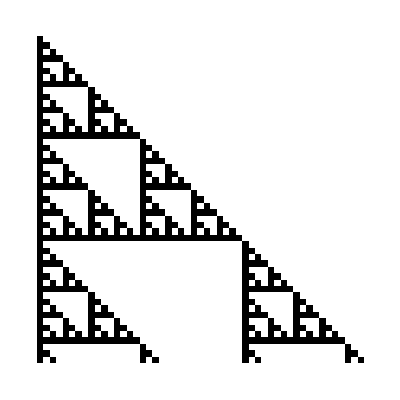

```mathematica
ArrayPlot[NestList[Mod[Join[{0},#]+Join[#,{0}],2]&,{1},50]]
```

```mathematica
ArrayPlot[NestList[Join[{0},#]+Join[#,{0}]+Join[#,RandomChoice[{Red,Green,Blue,Yellow,Orange,Pink,Cyan,Magenta}]]&,{1},50]]
```

Join::heads: Heads List and RGBColor at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

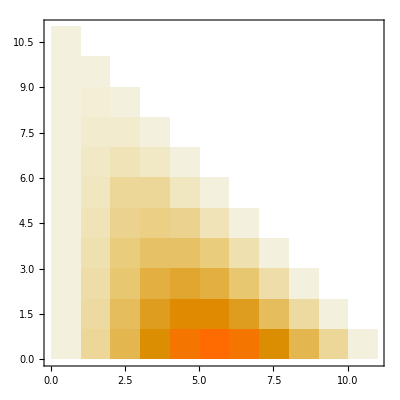

```mathematica
MatrixPlot[NestList[Join[{0}, #] + Join[#, {0}] &, {1}, 10]]
```

Generate a graph by starting from 0, then nestedly 10 times connecting each node with value n to ones with values n+1 and 2n. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
NestList[#->2,0,10]
```

{0,(#1→2)[0],(#1→2)[(#1→2)[0]],(#1→2)[(#1→2)[(#1→2)[0]]],(#1→2)[(#1→2)[(#1→2)[(#1→2)[0]]]],(#1→2)[(#1→2)[(#1→2)[(#1→2)[(#1→2)[0]]]]],(#1→2)[(#1→2)[(#1→2)[(#1→2)[(#1→2)[(#1→2)[0]]]]]],(#1→2)[(#1→2)[(#1→2)[(#1→2)[(#1→2)[(#1→2)[(#1→2)[0]]]]]]],(#1→2)[(#1→2)[(#1→2)[(#1→2)[(#1→2)[(#1→2)[(#1→2)[(#1→2)[0]]]]]]]],(#1→2)[(#1→2)[(#1→2)[(#1→2)[(#1→2)[(#1→2)[(#1→2)[(#1→2)[(#1→2)[0]]]]]]]]],(#1→2)[(#1→2)[(#1→2)[(#1→2)[(#1→2)[(#1→2)[(#1→2)[(#1→2)[(#1→2)[(#1→2)[0]]]]]]]]]]}

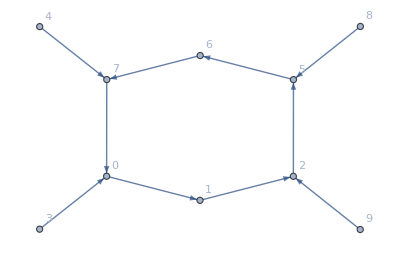

```mathematica
NestGraph[Mod[#^2 + 1, 10] &, Range[0, 9], VertexLabels -> Automatic]
```

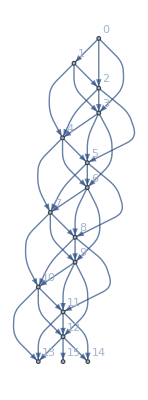

```mathematica
NestGraph[{#+1,#+2,#+3}&,0,5,VertexLabels -> Automatic]
```

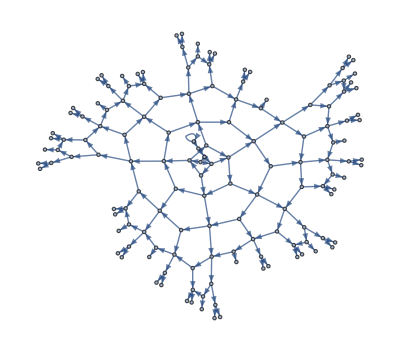

```mathematica
NestGraph[{#+1,2*#}&, 0,10]
```

Generate a graph obtained by nestedly finding bordering countries starting from the United States, and going 4 iterations. |

EXPECTED OUTPUT »

-Graphics- | ×

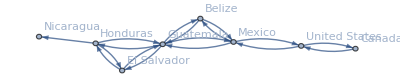

```mathematica
NestGraph[#["BorderingCountries"]&,Entity["Country","UnitedStates"],4,VertexLabels->All]
```

Make a line plot of 100 iterations of linear congruential function Mod[59#,101]&, starting from 1. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot@NestList[Mod[59*#,101]&,1,100]
```

-Graphics-

Create a list of 5 power towers of 2, i.e. 2^2^2...^2 n times, with n from 0 to 4. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
NestList[2^#&,1,4]
```

{1,2,4,16,65536}

Create a list of 20 power towers of 1.2, i.e. 1.2^1.2^...^1.2  n times, with n from 0 to 19. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
NestList[1.2^#&,1,19]
```

{1,1.2,1.24456,1.25472,1.25704,1.25758,1.2577,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773}

```mathematica
ListPlot[{1,1.2,1.24456,1.25472,1.25704,1.25758,1.2577,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773}]
```

-Graphics-

```mathematica
ListLinePlot[{1,1.2,1.24456,1.25472,1.25704,1.25758,1.2577,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773}]
```

-Graphics-

Generate a list of the numerical values obtained by up to 10 nestings of the function Sqrt[1+#]&. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
NestList[Sqrt[1+#]&,1,10]//N
```

{1.,1.41421,1.55377,1.59805,1.61185,1.61612,1.61744,1.61785,1.61798,1.61802,1.61803}

```mathematica
ListPlot[NestList[Sqrt[1+#]&,1,10]//N]
```

-Graphics-

```mathematica
ListPlot[(NestList[1.2^#&,1,50])-(NestList[Sqrt[1+#]&,1,50]//N)]
```

-Graphics-

Make graphics of a 1000-step 3D random walk which starts at {0,0,0}, and in which at each step a triple of random numbers between −1 and +1 are added to the coordinates. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
NestList[#+1&,{0,0},10]
```

{{0,0},{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10}}

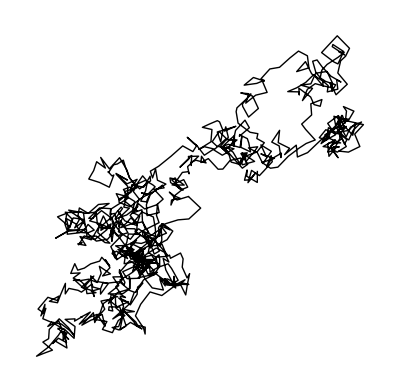

```mathematica
Graphics@Line[NestList[#+RandomReal[{-1,1},2]&,{0,0},1000]]
```

```mathematica
Graphics@Line[NestList[#+RandomReal[{-1,1},3]&,{0,0,0},1000]]
```

-Graphics-

```mathematica
Graphics3D@Line@NestList[#+RandomReal[{-1,1},3]&,{0,0,0},1000]
```

-Graphics3D-

```mathematica
Graphics[%31]
```

-Graphics-